# 镂空曲面 - RegionFunction

### https : // community . wolfram . com/groups/-/m/t/2142619

```mathematica
a=0.65;
expression=(x^2+y^2-a^2)^3-a x^2 y^3/.{x->Sin[12u^2],y->Cos[12v^2]}
```

```mathematica
ParametricPlot3D[{Sin[v](15Sin[u]-4 Sin[3 u]),8Cos[v],Sin[v](15Cos[u]-5 Cos[2u]-2 Cos[3 u]-Cos[2 u])},{u,-π,π},{v,0,π},Mesh->None,Boxed->True,Axes->True,PlotStyle->{Red,Specularity[White,80]},MaxRecursion->4,PlotPoints->80,RegionFunction->Function[{x,y,z,u,v},-0.75 Cos[12 v]^3 Sin[12 u]^2+(-0.5625+Cos[12 v]^2+Sin[12 u]^2)^3>=0],PlotTheme->"ThickSurface",ViewPoint->Front,AxesLabel->{"x","y","z"},PlotLabel->Style["mapping heart curve on heart surface",14,Bold],ImageSize->350{1,1}]
```

-Graphics3D-

### 其中的思路

```mathematica
ParametricPlot3D[{Cos[u]Cos[v],Sin[u]Cos[v],Sin[v]},{u,0,Pi},{v,0,2Pi},PlotTheme->"ThickSurface",RegionFunction->Function[{x,y,z,u,v},-.5<Cos[3 u]+Sin[3 v]<0.5]]
```

-Graphics3D-

注意下面u的范围

```mathematica
ParametricPlot3D[{Cos[u]Cos[v],Sin[u]Cos[v],Sin[v]},{u,0,2Pi},{v,0,2Pi},PlotTheme->"ThickSurface",RegionFunction->Function[{x,y,z,u,v},Cos[3 u]Sin[5 v]>0.5],PlotPoints->50]
```

-Graphics3D-

修改参数表达式

```mathematica
ParametricPlot3D[{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]},{u,0,2Pi},{v,0,Pi},PlotTheme->"ThickSurface",RegionFunction->Function[{x,y,z,u,v},-.5<Cos[3 u]Sin[5 v]<0.5],PlotPoints->50]
```

-Graphics3D-

```mathematica
p3d=ParametricPlot3D[{Cos[u]Cos[v],Sin[u]Cos[v],Sin[v]},{u,0,Pi},{v,0,2Pi},PlotTheme->"ThickSurface",RegionFunction->Function[{x,y,z,u,v},-.5<Cos[3 u]Sin[5 v]<.5],PlotPoints->50]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]},{u,0,2Pi},{v,0,Pi},PlotTheme->"ThickSurface",RegionFunction->Function[{x,y,z,u,v},-.5<Cos[5 u]<.5||-.5<Sin[6 v]<.5],PlotPoints->50]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]}(1+0.2Cos[5u]Cos[5v]),{u,0,2Pi},{v,0,Pi},PlotTheme->"ThickSurface",RegionFunction->Function[{x,y,z,u,v},-.5<Cos[5 u]<.5||-.5<Sin[6 v]<.5],PlotPoints->50]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]}(1+0.3Cos[5u]+0.3Cos[5v]),{u,0,2Pi},{v,0,Pi},PlotTheme->"ThickSurface",RegionFunction->Function[{x,y,z,u,v},-.5<Cos[5 u]<.5||-.5<Sin[6 v]<.5],PlotPoints->50,PlotStyle->MaterialShading["Silver"],Lighting->"ThreePoint"]
```

-Graphics3D-

### 使用MeshFunction

```mathematica
ParametricPlot3D[{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]},{u,0,2Pi},{v,0,Pi},MeshShading->{{Automatic,Automatic},{Automatic,None}},PlotPoints->50,PlotStyle->Thick,MeshStyle->Transparent]
```

-Graphics3D-

```mathematica
壳
```

```mathematica
Table[ParametricPlot3D[{x,y,Cos[x]~op~ Sin[y]},{x,-2Pi,2Pi},{y,-2Pi,2Pi}],{op,{Plus,Subtract,Times}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[ParametricPlot3D[{x,y,Clip[Cos[x]~op~Sin[y],{-.5,.5}]},{x,-2Pi,2Pi},{y,-2Pi,2Pi}],{op,{Plus,Subtract,Times}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ParametricPlot3D[{x,y,Clip[3Cos[x]Sin[y],{-.5,.5}]},{x,0,2Pi},{y,0,2Pi},PlotPoints->90]
```

-Graphics3D-

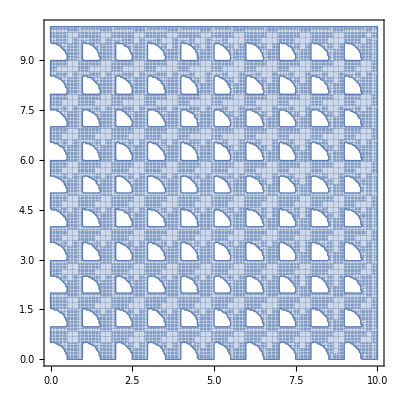

```mathematica
ParametricPlot[{u,v},{u,0,10},{v,0,10},RegionFunction->Function[{x,y,u,v},Norm[{Floor[u],Floor[v]}-{u,v}]>0.5],PlotPoints->60]
```

```mathematica
Manipulate[ParametricPlot[{u,v},{u,0,10},{v,0,10},RegionFunction->Function[{x,y,u,v},Norm[{Round[u,a],Round[v,a]}-{u,v}]>r],PlotPoints->60],{a,1,10,1},{r,0.5,5}]
```

### 我们可以根据仰角来调整小圆的半径

```mathematica
s[u_,v_,r_:1]:=r{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]}
Manipulate[ParametricPlot3D[s[u,v,r],{u,0,2Pi},{v,0,Pi},RegionFunction->Function[{x,y,z,u,v},Norm[s[Round[u,au],Round[v,av],r]-s[u,v,r]]>rF Sin[v]],PlotPoints->60],{{r,5},1,10},{{au,1},3,0.1,-0.1},{{av,1},3,0.1,-0.1},{{rF,0.5},0.1,5}]
```

```mathematica
s[u_,v_]:=9{Sin[u]Sin[v],Cos[u]Sin[v],Cos[v]}
ParametricPlot3D[s[u,v],{u,0,2Pi},{v,0,Pi},RegionFunction->({x,y,z,u,v}|->Norm[s[Round[u,Pi/8],Round[v,.35]]-s[u,v]]>Sin[v]),PlotPoints->60,PlotTheme->{"ThickSurface","NoAxes"},PlotStyle->{Orange,Specularity[Pink,30]}]
```

-Graphics3D-

### 如何使得每一层的圆孔数量自动的调整，其半径不变

### 先来思考一个这样的问题 对于给定的圆半径R和弦长的一半r，不会交叉的弦的最大数量n是多少？

```mathematica
pts[R_,r_,n_]:=Block[{θ,ϕ,l},θ=2ArcSin[r/R];ϕ=(2π)/n-θ;l=Riffle[Table[θ,n],ϕ];(*(RotationMatrix[#].{1,0}&/@Prepend[Accumulate[l],0])*)FoldList[RotationMatrix[#2].#1&,{1,0},l]]
Manipulate[p=pts[R,r,n];Graphics[{Circle[],Thick,Orange,Line[Partition[p,2]],Magenta,PointSize[Large],Point@p}],{{R,1},r,5},{{r,.5},.1,R},{{n,3},2,10,1}]
```

### 我在纸上推到出他们的关系应为 n=Floor[Rπ/r]

```mathematica
DynamicModule[{p},Manipulate[p=pts[R,r,Floor[R π/r]];Graphics[{Circle[],Thick,Orange,Line[Partition[p,2]],Magenta,PointSize[Large],Point@p},PlotLabel->R π/r],{{R,1},r,5},{{r,.5},.1,R}]]
```

### 看来还不够理想，那么问题出现在哪里呢？

根据逻辑关系列出如下不等式
2 r n < 2 R π  < 2 r (n+1)
可得出Rπ/r-1<n<Rπ/r
因为n是整数，所以得出n=Floor[Rπ/r]
但存在这样一种情况，弦刚刚发生交叉，而弦长之和并未超过圆的周长

### 一种正确的思路

n=Floor[π/ArcSin[r/R]]

```mathematica
DynamicModule[{p,n},Manipulate[n=Floor[π/ArcSin[r/R]];p=pts[R,r,n];Graphics[{Circle[],Thick,Orange,Line[Partition[p,2]],Magenta,PointSize[Large],Point@p},PlotLabel->n],{{R,1},r,5},{{r,.5},.1,R}]]
```

### 现在，我们可以继续在球面上挖洞了

暂时让小孔的半径为1

```mathematica
s[u_,v_]:=9{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]}
ParametricPlot3D[s[u,v],{u,0,2Pi},{v,0,Pi},RegionFunction->({x,y,z,u,v}|->Norm[s[Round[u,4π/Floor[π/ArcSin[1/(9Sin[v]+0.001)]]],Round[v,.35]]-s[u,v]]>Sin[v]),PlotPoints->60,PlotTheme->{"NoAxes"},PlotStyle->{Orange,Specularity[Pink,30]}]
```

Power::infy: 碰到无穷表达式 1/0.

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

-Graphics3D-